```mathematica
<<MB.m
```

MB 1.2

by Michal Czakon

improvements by Alexander Smirnov

more info in hep-ph/0511200

last modified 2 Jan 09

```mathematica
<<AMBREv1.2.m
```

by K.Kajda   ver: 1.2 
last modified 9 Apr 2008
last executed on 16.05.2022 at 11:47

```mathematica
<<PlanarityTestv1.2.1.m
```

by E. Dubovyk and K. Bielas ver: 1.2.1
created: Aug 2017
last executed: 16.05.2022 at 11:47

```mathematica
<<AMBREv2.1.1.m
```

AMBRE by K.Kajda   ver: 2.1.1 
last modified Aug 2017

```mathematica
<<barnesroutines.m
```

Barnes Routines, v 1.1.1 of July 23, 2009

SetDelayed::write: Tag Merge in Merge[{MB`MBint[int1_,contour1_,origins1___],MB`MBint[int2_,contour2_,origins2___]}] is Protected.

```mathematica
<<MBasymptotics.m
```

```mathematica
invariants={p1^2->s};
```

```mathematica
repr=PR[k1,m,n1]*PR[k1+p1,m,n2];
```

Contract::shdw: Symbol Contract appears in multiple contexts {Combinatorica`,AMBRE`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

The Diagram

is planar.

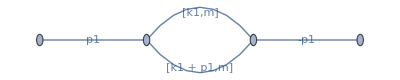

```mathematica
PlanarityTest[{repr},{k1},DrawGraph->True];
```

```mathematica
repr1=MBrepr[{1},{repr},{k1}]
```

>>External momenta = N/A

>>Starting LoopByLoop calculation

--iteration nr: 1 with momentum: k1

Run ?INT to see description of below output 
{INT[{1},1,PR[k1,m,n1] PR[k1+p1,m,n2],N/A]}

F polynomial during this iteration 
m^2 FX[X[1]+X[2]]^2-s X[1] X[2]

>>Contracting and finalizing output

--contracting...

--finalizing output...

>>Checking Barnes 1-st lemma...

{((-1)^(n1+n2) (m^2)^z1 (-s)^(-eps-n1-n2-z1) s^2 Gamma[2-eps-n1-z1] Gamma[2-eps-n2-z1] Gamma[-z1] Gamma[-2+eps+n1+n2+z1])/(Gamma[n1] Gamma[n2] Gamma[4-2 eps-n1-n2-2 z1])}

```mathematica
finres=repr1[[1]]/.{n1->1,n2->1}
```

((m^2)^z1 (-s)^(-2-eps-z1) s^2 Gamma[1-eps-z1]^2 Gamma[-z1] Gamma[eps+z1])/Gamma[2-2 eps-2 z1]

```mathematica
SE2l2m=%/.n1->1/.n2->1
```

((m^2)^z1 (-s)^(-2-eps-z1) s^2 Gamma[1-eps-z1]^2 Gamma[-z1] Gamma[eps+z1])/Gamma[2-2 eps-2 z1]

```mathematica
backGamma={G1[x__]->Gamma[x],G2[x__]->Gamma[x],G3[x__]->Gamma[x],G4[x__]->Gamma[x],G5[x__]->Gamma[x],G6[x__]->Gamma[x],G7[x__]->Gamma[x],G8[x__]->Gamma[x],G9[x__]->Gamma[x],G10[x__]->Gamma[x],G11[x__]->Gamma[x],G12[x__]->Gamma[x]};
```

```mathematica
aux=ms^z1 G1[1-eps-z1] G2[-z1] G3[eps+z1];
```

```mathematica
aux/.{eps->1,z1->-1/2}
```

(G1[1/2] G2[1/2] G3[1/2])/(√ms)

```mathematica
Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0
```

{1-eps-z1>0,-z1>0,eps+z1>0}

```mathematica
FindInstance[Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0/.eps->-1/2,{z1}]
```

{}

```mathematica
FindInstance[Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0/.eps->0,{z1}]
```

{}

```mathematica
FindInstance[Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0/.eps->1/2,{z1}]
```

{{z1→-1/4}}

```mathematica
subst=%[[1]]
```

{z1→-1/4}

```mathematica
subst0=Append[subst,eps->0]
```

{z1→-1/4,eps→0}

```mathematica
aux/.subst/.eps->1/2
```

(G1[3/4] G2[1/4] G3[1/4])/ms^(1/4)

```mathematica
aux/.subst0
```

(G1[5/4] G2[1/4] G3[-1/4])/ms^(1/4)

G3 changes sign, goes through a pole

```mathematica
aux
```

ms^z1 G1[1-eps-z1] G2[-z1] G3[eps+z1]

```mathematica
res0=Residue[SE2l2m,{z1,-eps}]
```

(m^2)^-eps Gamma[eps]

```mathematica
res1=Residue[SE2l2m,{z1,0}]
```

-((-s)^-eps Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]

```mathematica
res2=Residue[SE2l2m,{z1,1-eps}]
```

(2 (m^2)^(1-eps) Gamma[-1+eps])/s

Sometimes it can happen with MB . m

```mathematica
rules=MBoptimizedRules[SE2l2m,eps->0,{},{eps}]
```

MBrules::norules: no rules could be found to regulate this integral

{{eps→1},{z1→-1/2}}

We can take a different z1 value

```mathematica
rules=MBoptimizedRules[SE2l2m,eps->0,{z1>-1/4},{eps}]
```

MBrules::norules: no rules could be found to regulate this integral

{{eps→5/8},{z1→-1/8}}

Re[eps] and Re[z1] makes integral well defined : arguments of Gamma functions are positive

```mathematica
Numerator[SE2l2m/((m^2)^z1 (-s)^(-eps-z1))/.Gamma[x_]->gamma[x]]/.Flatten[rules]
```

gamma[1/8] gamma[1/2]^3

```mathematica
?FindInstance
```

RowBox[{"FindInstance", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] finds an instance of StyleBox["vars", "TI"] that makes the statement StyleBox["expr", "TI"] be True. 
RowBox[{"FindInstance", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] finds an instance over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Complexes, Reals, Integers and Booleans. 
RowBox[{"FindInstance", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"], ",", StyleBox["n", "TI"]}], "]"}] finds StyleBox["n", "TI"] instances.

```mathematica
num=Gamma[1-eps-z1] Gamma[-z1] Gamma[eps+z1]
```

Gamma[1-eps-z1] Gamma[-z1] Gamma[eps+z1]

```mathematica
Cases[num,Gamma[_]]/.Gamma[x_]->x>0
```

{1-eps-z1>0,-z1>0,eps+z1>0}

```mathematica
{1-eps-z1>0,-z1>0,eps+z1>0}
```

{1-eps-z1>0,-z1>0,eps+z1>0}

```mathematica
FindInstance[%,{eps,z1}]
```

{{eps→3/2,z1→-1}}

Now analytic continuation in eps -> 0

```mathematica
integrals=MBcontinue[SE2l2m,eps->0,rules]
```

Level 1

Taking +residue in z1 = -eps

Level 2

Integral {1}

2 integral(s) found

{{MBint[(m^2)^-eps Gamma[eps],{{eps→0},{}}]},MBint[((m^2)^z1 (-s)^(-2-eps-z1) s^2 Gamma[1-eps-z1]^2 Gamma[-z1] Gamma[eps+z1])/Gamma[2-2 eps-2 z1],{{eps→0},{z1→-1/8}}]}

In MB_B5l2m2_Springer.nb we will show how analytic continuation works algorithmically

```mathematica
ser=MBexpand[integrals,Exp[eps*EulerGamma],{eps,0,0}]
```

{MBint[1/eps-Log[m^2],{{eps→0},{}}],MBint[((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1],{{eps→0},{z1→-1/8}}]}

```mathematica
{MBint[((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1],{{eps->0},{z1->-1/8}}]}//InputForm
```

{MBint[((m^2)^z1*Gamma[1 - z1]^2*Gamma[-z1]*Gamma[z1])/((-s)^z1*Gamma[2 - 2*z1]), {{eps -> 0}, {z1 -> -1/8}}]}

```mathematica
ser={MBint[((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1],{{eps->0},{z1->-1/8}}]};
```

```mathematica
ser//InputForm
```

{MBint[((m^2)^z1*Gamma[1 - z1]^2*Gamma[-z1]*Gamma[z1])/((-s)^z1*Gamma[2 - 2*z1]), {{eps -> 0}, {z1 -> -1/8}}]}

```mathematica
num1=MBintegrate[ser,{s->-100,m->1}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{-2.71646729046132,0}

```mathematica
num2=MBintegrate[ser,{s->-1/100,m->1}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{-0.00166500237699269,0}

Actually there is one parameter ms in ser

```mathematica
ser[[1,1]]/.(m^2)^z1 (-s)^-z1->ms^z1
```

(ms^z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1]

```mathematica
ser
```

{MBint[((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1],{{eps→0},{z1→-1/8}}]}

```mathematica
ser/.(m^2)^z1 (-s)^-z1->ms^z1
```

{MBint[{(ms^z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1]},{{eps→0},{z1→-1/8}}]}

```mathematica
?MBasymptotics
```

```mathematica
after=ser/.(m^2)^z1 (-s)^-z1->ms^z1/.MBint[args__]:>MBasymptotics[MBint[args],{ms,5}]//MBmerge
```

{MBint[2-2 ms-ms^2+(10 ms^3)/3-(59 ms^4)/6+(449 ms^5)/15+(1+2 ms-2 ms^2+4 ms^3-10 ms^4+28 ms^5) Log[ms],{{eps→0},{}}]}

```mathematica
%//InputForm
```

{MBint[2 - 2*ms - ms^2 + (10*ms^3)/3 - (59*ms^4)/6 + (449*ms^5)/15 + (1 + 2*ms - 2*ms^2 + 4*ms^3 - 10*ms^4 + 28*ms^5)*Log[ms], {{eps -> 0}, {}}]}

```mathematica
(* Q: can we sum up residues to Infinity? *)
```

```mathematica
(* A: surely, not directly *)
```

```mathematica
Sum[Residue[ser[[1,1,1]],{z1,i}],{i,0,Infinity}]
```

0

Approximations, closing on right - half in a complex plane, means s >> m^2

```mathematica
-Residue[ser[[1,1]],{z1,0}]//InputForm
```

2 + Log[m^2] - Log[-s]

```mathematica
-Residue[ser[[1,1]],{z1,1}]/.m->1
```

-(2 (-1-Log[-s]))/s

```mathematica
-Residue[ser[[1,1]],{z1,1}]//InputForm
```

(-2*(-m^2 + m^2*Log[m^2] - m^2*Log[-s]))/s

```mathematica
-Residue[ser[[1,1]],{z1,2}]//InputForm
```

-((m^4 + 2*m^4*Log[m^2] - 2*m^4*Log[-s])/s^2)

```mathematica
-Residue[ser[[1,1]],{z1,2}]/.m->1
```

-(1-2 Log[-s])/s^2

```mathematica
sum=Sum[-Residue[ser[[1,1]],{z1,i}],{i,0,10}]
```

2+Log[m^2]-Log[-s]-(2 (-m^2+m^2 Log[m^2]-m^2 Log[-s]))/s-(m^4+2 m^4 Log[m^2]-2 m^4 Log[-s])/s^2-(2 (5 m^6+6 m^6 Log[m^2]-6 m^6 Log[-s]))/(3 s^3)-(59 m^8+60 m^8 Log[m^2]-60 m^8 Log[-s])/(6 s^4)-(449 m^10+420 m^10 Log[m^2]-420 m^10 Log[-s])/(15 s^5)-(1417 m^12+1260 m^12 Log[m^2]-1260 m^12 Log[-s])/(15 s^6)-(2 (16127 m^14+13860 m^14 Log[m^2]-13860 m^14 Log[-s]))/(105 s^7)-(429697 m^16+360360 m^16 Log[m^2]-360360 m^16 Log[-s])/(420 s^8)-(5 (87541 m^18+72072 m^18 Log[m^2]-72072 m^18 Log[-s]))/(126 s^9)-(7549093 m^20+6126120 m^20 Log[m^2]-6126120 m^20 Log[-s])/(630 s^10)

```mathematica
sum=2+Log[m^2]-Log[-s]-(2 (-m^2+m^2 Log[m^2]-m^2 Log[-s]))/s-(m^4+2 m^4 Log[m^2]-2 m^4 Log[-s])/s^2-(2 (5 m^6+6 m^6 Log[m^2]-6 m^6 Log[-s]))/(3 s^3)-(59 m^8+60 m^8 Log[m^2]-60 m^8 Log[-s])/(6 s^4)-(449 m^10+420 m^10 Log[m^2]-420 m^10 Log[-s])/(15 s^5)-(1417 m^12+1260 m^12 Log[m^2]-1260 m^12 Log[-s])/(15 s^6)-(2 (16127 m^14+13860 m^14 Log[m^2]-13860 m^14 Log[-s]))/(105 s^7)-(429697 m^16+360360 m^16 Log[m^2]-360360 m^16 Log[-s])/(420 s^8)-(5 (87541 m^18+72072 m^18 Log[m^2]-72072 m^18 Log[-s]))/(126 s^9)-(7549093 m^20+6126120 m^20 Log[m^2]-6126120 m^20 Log[-s])/(630 s^10);
```

```mathematica
sum/.m->1/.Log[x_]->0
```

2-7549093/(630 s^10)-437705/(126 s^9)-429697/(420 s^8)-32254/(105 s^7)-1417/(15 s^6)-449/(15 s^5)-59/(6 s^4)-10/(3 s^3)-1/s^2+2/s

```mathematica
nologs=sum/.m->1/.Log[x_]->0
```

2-7549093/(630 s^10)-437705/(126 s^9)-429697/(420 s^8)-32254/(105 s^7)-1417/(15 s^6)-449/(15 s^5)-59/(6 s^4)-10/(3 s^3)-1/s^2+2/s

```mathematica
logs=Coefficient[sum,Log[-s]]/.m->1
```

-1+9724/s^10+2860/s^9+858/s^8+264/s^7+84/s^6+28/s^5+10/s^4+4/s^3+2/s^2+2/s

```mathematica
Sum[-Residue[ser[[1,1]],{z1,i}],{i,0,Infinity}]
```

0

```mathematica
sum/.m->1/.s->-100//N
```

-2.71647

```mathematica
num1
```

{-2.71646729046132,0}

Building the Ansatz for analytic solution of `unknown’, Chapter 5, Eq . 5.183

```mathematica
unknown=((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1]
```

((m^2)^z1 (-s)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1]

```mathematica
unknown//InputForm
```

((m^2)^z1*Gamma[1 - z1]^2*Gamma[-z1]*Gamma[z1])/((-s)^z1*Gamma[2 - 2*z1])

```mathematica
unknown/.m->1/.s->-((1-y)^2/y)
```

(((1-y)^2/y)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1]

```mathematica
fun=(((1-y)^2/y)^-z1 Gamma[1-z1]^2 Gamma[-z1] Gamma[z1])/Gamma[2-2 z1];
```

```mathematica
sumresid=Sum[-Residue[fun,{z1,i}],{i,0,10}];
```

```mathematica
serEq2=Normal[Series[sumresid,{y,0,10}]]//Simplify;
```

```mathematica
serEq2
```

2+(1+2 y+2 y^2+2 y^3+2 y^4+2 y^5+2 y^6+2 y^7+2 y^8+2 y^9+2 y^10) Log[y]

```mathematica
serEq2=2+(1+2 y+2 y^2+2 y^3+2 y^4+2 y^5+2 y^6+2 y^7+2 y^8+2 y^9+2 y^10) Log[y]
```

2+(1+2 y+2 y^2+2 y^3+2 y^4+2 y^5+2 y^6+2 y^7+2 y^8+2 y^9+2 y^10) Log[y]

```mathematica
poly[x_]={x,1,1/(1-x),1/(1+x)};
```

```mathematica
baseHPL={1, Log[y] }
```

{1,Log[y]}

```mathematica
baseHPL=Union[
Join[{Zeta[2],PolyLog[2,y]},Flatten[Outer[Times,{Log[y],Log[1-y]},{Log[y],Log[1-y]}]]]]
```

{π^2/6,Log[1-y]^2,Log[1-y] Log[y],Log[y]^2,PolyLog[2,y]}

```mathematica
basis=Flatten[Map[#*poly[y]&,baseHPL]]
```

{y,1,1/(1-y),1/(1+y),y Log[y],Log[y],Log[y]/(1-y),Log[y]/(1+y)}

```mathematica
Length[basis]
```

8

```mathematica
eq=Array[c,Length[basis]].basis
```

y c[1]+c[2]+c[3]/(1-y)+c[4]/(1+y)+y c[5] Log[y]+c[6] Log[y]+(c[7] Log[y])/(1-y)+(c[8] Log[y])/(1+y)

```mathematica
serEq1=Normal[Series[eq,{y,0,10}]];
```

```mathematica
serEq2
```

2+(1+2 y+2 y^2+2 y^3+2 y^4+2 y^5+2 y^6+2 y^7+2 y^8+2 y^9+2 y^10) Log[y]

```mathematica
2+(1+2  y/(1-y))Log[y]//Simplify
```

2-((1+y) Log[y])/(-1+y)

```mathematica
%//InputForm
```

2 - ((1 + y)*Log[y])/(-1 + y)

```mathematica
nologs=serEq1-serEq2/.a_. Log[y]^_.->0;
```

```mathematica
nologs
```

-2+c[2]+c[3]+y^3 (c[3]-c[4])+y^5 (c[3]-c[4])+y^7 (c[3]-c[4])+y^9 (c[3]-c[4])+y (c[1]+c[3]-c[4])+c[4]+y^2 (c[3]+c[4])+y^4 (c[3]+c[4])+y^6 (c[3]+c[4])+y^8 (c[3]+c[4])+y^10 (c[3]+c[4])

```mathematica
logs=serEq1-serEq2-nologs//Simplify;
```

```mathematica
logs
```

(-1+c[6]+c[7]+y^3 (-2+c[7]-c[8])+y^5 (-2+c[7]-c[8])+y^7 (-2+c[7]-c[8])+y^9 (-2+c[7]-c[8])+y (-2+c[5]+c[7]-c[8])+c[8]+y^2 (-2+c[7]+c[8])+y^4 (-2+c[7]+c[8])+y^6 (-2+c[7]+c[8])+y^8 (-2+c[7]+c[8])+y^10 (-2+c[7]+c[8])) Log[y]

```mathematica
Table[0==Coefficient[nologs,y,i-1],{i,10}]
```

{0==-2+c[2]+c[3]+c[4],0==c[1]+c[3]-c[4],0==c[3]+c[4],0==c[3]-c[4],0==c[3]+c[4],0==c[3]-c[4],0==c[3]+c[4],0==c[3]-c[4],0==c[3]+c[4],0==c[3]-c[4]}

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[1]→0,c[2]→2,c[3]→0,c[4]→0}}

```mathematica
rule1=%[[1]]
```

{c[1]→0,c[2]→2,c[3]→0,c[4]→0}

```mathematica
Coefficient[serEq1,c[9]]//Simplify
```

0

```mathematica
Table[0==Coefficient[logs,y,i-1],{i,10}];
```

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[5]→0,c[6]→-1,c[7]→2,c[8]→0}}

```mathematica
rule2=%[[1]]
```

{c[5]→0,c[6]→-1,c[7]→2,c[8]→0}

```mathematica
eq/.rule1/.rule2//Simplify
```

2-((1+y) Log[y])/(-1+y)

```mathematica
(* larger base *)
```

```mathematica
poly[x_]={x,1,1/(1-x),1/(1+x)};
```

```mathematica
baseHPL=Union[
Join[{Zeta[2],PolyLog[2,y]},Flatten[Outer[Times,{Log[y],Log[1-y]},{Log[y],Log[1-y]}]]]]
```

{π^2/6,Log[1-y]^2,Log[1-y] Log[y],Log[y]^2,PolyLog[2,y]}

```mathematica
?LatexForm
```

Global`LatexForm

```mathematica
{π^2/6,Log[1-y]^2,Log[1-y] Log[y],Log[y]^2,PolyLog[2,y]}//InputForm
```

{Pi^2/6, Log[1 - y]^2, Log[1 - y]*Log[y], Log[y]^2, PolyLog[2, y]}

```mathematica
basis=Flatten[Map[#*poly[y]&,baseHPL]]
```

{(π^2 y)/6,π^2/6,π^2/(6 (1-y)),π^2/(6 (1+y)),y Log[1-y]^2,Log[1-y]^2,Log[1-y]^2/(1-y),Log[1-y]^2/(1+y),y Log[1-y] Log[y],Log[1-y] Log[y],(Log[1-y] Log[y])/(1-y),(Log[1-y] Log[y])/(1+y),y Log[y]^2,Log[y]^2,Log[y]^2/(1-y),Log[y]^2/(1+y),y PolyLog[2,y],PolyLog[2,y],PolyLog[2,y]/(1-y),PolyLog[2,y]/(1+y)}

```mathematica
{(π^2 y)/6,π^2/6,π^2/(6 (1-y)),π^2/(6 (1+y)),y Log[1-y]^2,Log[1-y]^2,Log[1-y]^2/(1-y),Log[1-y]^2/(1+y),y Log[1-y] Log[y],Log[1-y] Log[y],(Log[1-y] Log[y])/(1-y),(Log[1-y] Log[y])/(1+y),y Log[y]^2,Log[y]^2,Log[y]^2/(1-y),Log[y]^2/(1+y),y PolyLog[2,y],PolyLog[2,y],PolyLog[2,y]/(1-y),PolyLog[2,y]/(1+y)}//InputForm
```

{(Pi^2*y)/6, Pi^2/6, Pi^2/(6*(1 - y)), Pi^2/(6*(1 + y)), y*Log[1 - y]^2, Log[1 - y]^2, Log[1 - y]^2/(1 - y), Log[1 - y]^2/(1 + y), y*Log[1 - y]*Log[y], Log[1 - y]*Log[y], 
 (Log[1 - y]*Log[y])/(1 - y), (Log[1 - y]*Log[y])/(1 + y), y*Log[y]^2, Log[y]^2, Log[y]^2/(1 - y), Log[y]^2/(1 + y), y*PolyLog[2, y], PolyLog[2, y], PolyLog[2, y]/(1 - y), PolyLog[2, y]/(1 + y)}

```mathematica
Length[basis]
```

20

```mathematica
eq=Array[c,Length[basis]].basis
```

1/6 π^2 y c[1]+1/6 π^2 c[2]+(π^2 c[3])/(6 (1-y))+(π^2 c[4])/(6 (1+y))+y c[5] Log[1-y]^2+c[6] Log[1-y]^2+(c[7] Log[1-y]^2)/(1-y)+(c[8] Log[1-y]^2)/(1+y)+y c[9] Log[1-y] Log[y]+c[10] Log[1-y] Log[y]+(c[11] Log[1-y] Log[y])/(1-y)+(c[12] Log[1-y] Log[y])/(1+y)+y c[13] Log[y]^2+c[14] Log[y]^2+(c[15] Log[y]^2)/(1-y)+(c[16] Log[y]^2)/(1+y)+y c[17] PolyLog[2,y]+c[18] PolyLog[2,y]+(c[19] PolyLog[2,y])/(1-y)+(c[20] PolyLog[2,y])/(1+y)

```mathematica
serEq1=Normal[Series[eq,{y,0,20}]];
```

10 residues is not enough  sumresid = Sum[-Residue[fun, {z1, i}], {i, 0, 10}];

```mathematica
sumresid=Sum[-Residue[fun,{z1,i}],{i,0,20}];
```

```mathematica
serEq2=Normal[Series[sumresid,{y,0,20}]]//Simplify;
```

```mathematica
nologs=serEq1-serEq2/.a_. Log[y]^_.->0;
```

```mathematica
nologs;
```

```mathematica
logs=serEq1-serEq2-nologs//Simplify;
```

```mathematica
Table[0==Coefficient[nologs,y,i-1],{i,20}];
```

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[1]→0,c[2]→12/π^2,c[3]→0,c[4]→0,c[5]→0,c[6]→0,c[7]→0,c[8]→0,c[17]→0,c[18]→0,c[19]→0,c[20]→0}}

```mathematica
rule1=%[[1]]
```

{c[1]→0,c[2]→12/π^2,c[3]→0,c[4]→0,c[5]→0,c[6]→0,c[7]→0,c[8]→0,c[17]→0,c[18]→0,c[19]→0,c[20]→0}

```mathematica
Table[0==Coefficient[logs,y,i-1],{i,20}];
```

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[9]→0,c[10]→0,c[11]→0,c[12]→0,c[13]→0,c[14]→-1/Log[y],c[15]→2/Log[y],c[16]→0}}

```mathematica
rule2=%[[1]]
```

{c[9]→0,c[10]→0,c[11]→0,c[12]→0,c[13]→0,c[14]→-1/Log[y],c[15]→2/Log[y],c[16]→0}

```mathematica
eq/.rule1/.rule2//Simplify
```

2-((1+y) Log[y])/(-1+y)

let us compare this series with an exact result known from elsewhere: e.g. DEqs method, see MastBhabhaEpsHPL.m

```mathematica
sE2l2m[0,x]=2-((1+x)*H[0,x])/(-1+x);
```

H[0, x] is so called harmonic polylogarithm function, class of functions introduced by Remiddi and Vermaseren, Chapters 2,5, eq.(5.176) and B_miscellaneous_Springer.nb

```mathematica
x[s_]:=(Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1);
```

The constant term

```mathematica
se=2-((1+x) Log[x])/(-1+x);
```

```mathematica
se /.x-> (Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1)
```

2-((1+(-1+√((-4+s)/s))/(1+√((-4+s)/s))) Log[(-1+√((-4+s)/s))/(1+√((-4+s)/s))])/(-1+(-1+√((-4+s)/s))/(1+√((-4+s)/s)))

```mathematica
se/.x->x[-100]//N
```

-2.71647

```mathematica
x/.x-> (Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1)
```

(-1+√((-4+s)/s))/(1+√((-4+s)/s))

```mathematica
%/.s->-((1-y)^2/y)
```

(-1+√(-((-4-(1-y)^2/y) y)/(1-y)^2))/(1+√(-((-4-(1-y)^2/y) y)/(1-y)^2))

```mathematica
%//FullSimplify
```

(-1+√((1+y)^2/(-1+y)^2))/(1+√((1+y)^2/(-1+y)^2))

```mathematica
%/.y->10.
```

0.1

We can make the same with the FF package (LoopTools)

```mathematica
(* 
 ====================================================FF 2.0,a package to evaluate one-loop integrals
written by G.J.van Oldenborgh,NIKHEF-H,Amsterdam
 ====================================================for the algorithms used see preprint NIKHEF-H 89/17,'New Algorithms for One-loop Integrals',by G.J.van
Oldenborgh and J.A.M.Vermaseren,published in
Zeitschrift fuer Physik C46(1990)425.
 ====================================================

        s = 100  (-2.49223029,3.07811959)
  Euclid, s = -100 (-2.71646729,0.)

total number of errors and warnings
===================================fferr:no errors
*)
```

Q : what about small s?

```mathematica
se/.x->x[-1/100]//N
```

-0.001665

```mathematica
sum/.m->1/.s->-1/100//N
```

-5.65974×10^24

Wrong! 
Q : what to do?
   A : close contour in negative half - plane : s << m^2

```mathematica
Sum[Residue[ser[[2,1]],{z1,-i}],{i,1,10}]
```

s/(6 m^2)+s^2/(60 m^4)+s^3/(420 m^6)+s^4/(2520 m^8)+s^5/(13860 m^10)+s^6/(72072 m^12)+s^7/(360360 m^14)+s^8/(1750320 m^16)+s^9/(8314020 m^18)+s^10/(38798760 m^20)

```mathematica
%/.m->1/.s->-1/100//N
```

-0.001665

```mathematica
se/.x->x[-1/100]//N
```

-0.001665

```mathematica
(************************************************ 
What we have shown are so called expansions of MB integrals, 
see e.g. M. Czakon, J.G., T.R., NPB751(2006)1
for more complicated cases and section 5.4
*************************************************)
```